The quantum three-body problem

In a basic course like Introduction to Modern Physics (that uses the Susskind pocket-book introduction to quantum physics), we put a lot of effort into describing and trying to understand two quantum particles, for example electrons. Here we start discussing the quantum three-body problem. 

(The word “body” from mechanics is better than the word “particle” here, since in quantum physics, particles can usually not be precisely localized, so think of them as “fuzzy”, which means effectively extended, even if they are point particles when measured.)

```mathematica
Needs["Wolfram`QuantumFramework`"]//Quiet
```

Two particles

From the Wolfram Quantum Framework help page,
here’s the predefined operator “Braid” on two qubits:
(recall the relation to spin is 0 = up, 1 = down).

```mathematica
B=QuantumOperator["Braid"]
```

1/(√2)0000+1/(√2)0011+1/(√2)0101+1/(√2)0110-1/(√2)1001+1/(√2)1010-1/(√2)1100+1/(√2)1111

(One can mean different things by “braid operator”. Think of this as a simple example, not some universal meaning of “braid operator” in quantum physics: we will see other examples below.)
As a matrix in this basis, B looks like:

```mathematica
BMatrix = B["Matrix"]//Normal
```

(1/(√2) | 0 | 0 | 1/(√2)
0 | 1/(√2) | 1/(√2) | 0
0 | -1/(√2) | 1/(√2) | 0
-1/(√2) | 0 | 0 | 1/(√2))

The Braid operator can be viewed as a transformation from the standard basis of 00,01,10,11 (called “computational basis” in quantum computing) to superposition (Bell) states:

```mathematica
AssociationMap[QuantumOperator["Braid"],QuantumBasis[2,2]["BasisStates"]]
```

<|00→1/(√2)00-1/(√2)11,01→1/(√2)01-1/(√2)10,10→1/(√2)01+1/(√2)10,11→1/(√2)00+1/(√2)11|>

In the permutation group S_2, we of course know that (12)^2 = e: if you exchange two particles twice, they have no memory of having been exchanged at all. 
Applying the braid operator twice, B^2, does not produce the identity:

```mathematica
BMatrix.BMatrix
```

(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)

So quantum particles can have “memory” that they have been exchanged: it is as if they had strings attached to them, like braids. This should not be too surprising if you have heard of the Aharonov-Bohm effect in a magnetic field, although here there is not necessarily a magnetic field.  

(Indeed, the information in the Nobel Prize for 2022 illustrates entanglement as strings attached between particles. However, there is no experimental evidence that there are any actual physical strings. The strings provide a way to illustrate quantum information with a classical drawing.) 

If we keep going, we see that B^4 = –I :

```mathematica
BMatrix.BMatrix.BMatrix.BMatrix
```

(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

so we’d need B^8 to literally get to the identity (we can identify the state with an overall sign with itself, so it depends on what we want to do). This is like a root of unity, q^8 = 1.

A more general way to characterize the generalization from 2 classical to 2 quantum particles is by replacing the symmetric group S_2 with the braid group B_2 ≃ ℤ, which has an infinite number of elements: a braid remembers how many times you twisted it. So B_2 is quite a lot more complicated than S_2 which is isomorphic to ℤ_2, and forgets immediately that it was ever applied, ℤ_2: {g,e} with g^2 = e. (The representation on qubits above, that terminates at B^8 = I, is not a representation of B_2, but of a quotient.)

Three (quasi-)particles
In the symmetric group S_n, everything can be built up from “local moves” among two particles at a time. Even then, something new appears compared to just two particles: S_3 is noncommutative. If we want a state to be uniquely described by specifying the numbering of the three particles, then we should demand (12)(23)(12)=(23)(12)(23), since both take the numbering 123 to 321. 

Comment: why “if” we want the state to be specified by the numbering? In local classical kinematics, with “no strings attached”, specifying the state by the numbering seems like a logical necessity. But in quantum mechanics, it could be viewed as a restriction that we choose to ignore whatever “memory” the strings might carry.

Consider R_12 : braid qubit 1 and 2, but do nothing to qubit 3. 
So R_12  = B ⊗ id:

```mathematica
R12=QuantumTensorProduct[r,QuantumOperator["I"]]
```

1/(√2)000000+1/(√2)000110+1/(√2)001001+1/(√2)001111+1/(√2)010010+1/(√2)010100+1/(√2)011011+1/(√2)011101-1/(√2)100010+1/(√2)100100-1/(√2)101011+1/(√2)101101-1/(√2)110000+1/(√2)110110-1/(√2)111001+1/(√2)111111

Now consider R_23 : braid qubit 2 and 3, but do nothing to qubit 1. 
So R_23  = id ⊗ B:

```mathematica
R23=QuantumTensorProduct[QuantumOperator["I"],r]
```

1/(√2)000000+1/(√2)000011+1/(√2)001001+1/(√2)001010-1/(√2)010001+1/(√2)010010-1/(√2)011000+1/(√2)011011+1/(√2)100100+1/(√2)100111+1/(√2)101101+1/(√2)101110-1/(√2)110101+1/(√2)110110-1/(√2)111100+1/(√2)111111

Check the Yang-Baxter equation:

```mathematica
(R12@R23@R12)==(R23@R12@R23)
```

True

OK. 
Comment: often (e.g. on Wikipedia, https://en.wikipedia.org/wiki/Yang%E2%80%93Baxter_equation) you see not (12)(23)(13)=(23)(12)(23) like here, but (12)(13)(23)=(23)(13)(12), using all three elements, including the “non-neighbor” move (13). As explained in the FYAD11 course notes and homework problems (at the time of writing, 1.9.7), to generate S_3 it’s enough to use local moves (exchange of neighbors). Using only nearest-neighbor exchanges is the Coxeter presentation of S_n:
https://en.wikipedia.org/wiki/Coxeter_group
For example in Zee’s book on group theory, he says “exchanges are the “atoms” out of which permutations are built”, but he doesn’t then restrict to local moves (I think). 

On a discrete lattice, allowing only local moves is sufficient to permute three classical objects, but amounts to what range we want to allow our interactions to have: nearest-neighbor, next-to-nearest neighbor, and so on. For more on this, see below.

Assemble a quantum circuit of Braid acting on successive states.
Here’s (23)(12)(23):

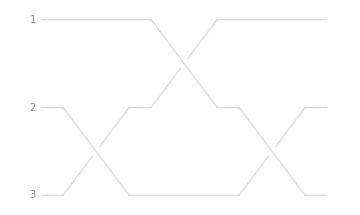

```mathematica
qc1=QuantumCircuitOperator[{"Braid"->{2,3},"Braid"->{1,2},"Braid"->{2,3}}];
qc1["Diagram"]
```

Here’s (12)(23)(13):

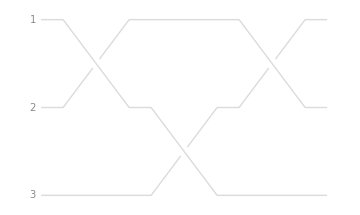

```mathematica
qc2=QuantumCircuitOperator[{"Braid"->{1,2},"Braid"->{2,3},"Braid"->{1,2}}];
qc2["Diagram"]
```

These circuits are equivalent as circuits:

```mathematica
qc1==qc2
```

True

OK.

At the top of this file, I wrote that we only “start” with the three-body problem here. By this I mean at least two things: 
1. The above is not general (or even close). It’s very far from describing all aspects of any of the three particles. Even for two particles, in basic courses we rarely attempt to describe all aspects of e.g. actual electrons simultaneously. What is done for example in the Intro Mod.Phys. course is to a) motivate the introduction of the basic object, the qubit, using the electron’s spin, b) switch to talking about the qubit as any two-state system abstractly. For example, maybe a more basic question about whether a particle has spin is whether it’s present at all: we can use the qubit to distinguish this, e.g. spin up = present, spin down = not present. (This is the Jordan-Wigner transformation, which I discuss elsewhere.)
2. The above is not final (or even close). By this I mean that teaching of basic quantum physics is evolving rapidly as we give these courses, with more about entanglement moving to earlier courses. There is no universally-agreed upon way to characterize entanglement for many-body systems. For two, entanglement entropy is enough, but already for three particles, nontrivial choices appear. For example, now the “environment” of any particle consists of two other particles, so should we take into account whether they are entangled among each other? 
Summary: the above is probably not how we will express these things in a few years from now. In fact in my opinion, no universally useful and complete way to describe three quantum particles is known, especially when interactions are taken into account. This should maybe not be so surprising, given the difficulty of the classical three-body problem!

[I have another Mathematica file on non-constant Yang-Baxter. I’m not sure it’s useful yet.]